# Contact angles

Contact angle measurements between inks used in
“Changes in filament microstructures during direct ink writing with yield stress fluid support”
“Printing direction dependent microstructure in direct ink writing”
“Corner accuracy in direct ink writing with support material”
Last updated November 2019 by Leanne Friedrich

```mathematica
ster[data_]:=If[Length[data]>1,N[StandardDeviation[data]/Sqrt[Length[data]]],0]
```

### on glass

```mathematica
adv20 = {60.29, 59.91, 61.58, 56.99, 61.56, 57.65, 61.46, 55.65, 59.54, 58.29, 60.65, 62.03, 59.74, 57.85, 65.69, 68.57, 64.57, 60.74, 52.57, 57.08, 55.13, 53.68, 56.76, 52.72, 58.68, 52.54, 54.89, 53.31, 59.49, 58.83, 58.54, 57.86};
rec20 ={21.72, 18.24, 16.30, 21.21, 18.31, 16.86, 17.29, 18.04, 15.18, 19.22, 18.29, 24.45, 17.01, 21.74, 21.14, 21.60, 17.34, 25.13, 19.46, 19.40, 18.65, 19.58, 17.77, 15.96, 16.81, 18.03 ,20.06, 18.78, 25.65, 22.22, 23.08, 25.02};
eq20 ={38.86, 43.42, 38.04, 42.73, 44.55, 43.65, 42.09, 45.07, 45.47, 47.28, 45.52, 47.84, 40.18, 41.92, 38.29, 41.61, 41.12, 40.49, 48.82, 45.19, 44.52, 51.24, 46.58, 47.61, 42.73, 36.99, 39.95, 40.57, 37.16, 39.21, 39.07, 40.42, 37.99, 43.00, 40.71, 40.01};
adv25 = {68.67, 67.07, 69.46, 69.03, 50.30, 59.04, 53.95, 49.29, 65.44, 60.38, 58.11, 63.81, 63.45, 60.20,  65.41, 63.81, 59.97, 61.83, 60.14, 63.72, 57.04, 65.37, 57.11, 63.82, 52, 56.31, 60.05, 57.90, 44.01, 48.79, 47.27, 46.82};
rec25 = {21.23, 21.03, 20.77, 24.90, 21.97, 21.21, 18.36, 21.08, 19.50, 17.58, 17.42, 19.00, 17.60, 21.24, 12.89, 16.78, 13.10, 25.13, 17.71, 15.31, 21.20, 19.80, 16.50, 18.36, 16.23, 17.06, 20.68, 20.57, 15.72, 18.43, 16.44, 17.89};
eq25 = {31.24, 36.49, 30.61, 36.32, 34.11, 37.59, 37.23, 33.60, 40.34, 39.41, 39.71, 35.15, 40.95, 45.82, 46.71, 41.44, 35.67, 39.64, 35.49, 34.07, 33.50, 41.16, 35.60, 37.34, 34.81, 39.57, 34.60, 35.16, 37.28, 36.52, 36.97, 37.19};
adv30 = {61.34, 65.73, 63.06, 61.99, 44.80, 51.99, 43.59, 49.67, 53.97, 57.30, 55.81, 60.23, 42.92, 43.41, 47.07, 45.32, 43.74, 44.25, 45.72, 44.55, 42.62, 46.89, 45.60, 47.48, 49.30, 46.89, 53.33, 51, 44.74, 46.88, 49.61, 43.71};
rec30 = {14.96, 16.02, 15.04, 12.13, 17.68, 20.91, 17.48, 16.62, 17.56, 17.06, 19.37, 14.64, 23.23, 20.05, 20.67, 24.13, 18.75, 14.85, 14.55, 13.44, 22.43, 18.01, 18.57, 18.34, 18.23, 20.76, 20.34, 22.73, 17.64, 20.89, 17.47, 20.21};
eq30 = {38.72, 34.89, 35.40, 33.57, 35.55, 33.92, 36.68, 33.32, 39.36, 40.97, 39.00, 39.88, 37.05, 38.78, 39.10, 39.68, 34.74, 33.91, 35.34, 32.49, 29.17, 33.65, 32.81, 28.59, 39.04, 35.86, 37.31, 33.38, 23.56, 25.43, 29.18, 23.69};
adv35 = {45.56, 43.85, 46.69, 39.70, 48.57, 49.38, 50.43, 45.79, 54.55, 52.06, 53.47, 51.21, 61.80, 60.79, 62.64, 62.12, 41.50, 41.99, 45.28, 42.22, 48.89, 49.60, 50.77, 51.12, 44.46, 44.84, 45.88, 45.67, 59.62, 59.17, 60.32, 56.67};
rec35 = {14.45, 11.18, 16.70, 9.52, 13.46, 14.37, 12.80, 8.59, 10.89, 9.83, 15.09, 10.20, 19.76, 16.74, 12.41, 9.15, 16.07, 15.38, 15.06, 12.65, 16.81, 14.36, 12.88, 10.57, 14.51, 15.96, 12.70, 9.27, 18.88, 18.12 ,13.72 ,9.14};
eq35 = {40.91, 39.11, 43.17, 42.15, 34.02, 32.65, 37.85, 33.21, 25.66, 27.91, 38.75, 25.57, 37.14, 38.75, 38.80, 40.13, 23.12, 22.00, 22.02 ,18.76, 38.93, 35.63, 34.93, 35.77, 34.36, 34.33, 32.79, 33.85, 27.10 ,26.07, 25.52, 24.80};
advc = {49.19, 51.40, 38.47, 28.29, 45.56, 48.54, 39.97, 41.44, 44.23, 50.99, 51.89,  52.09, 40.49, 42.61, 42.17, 43.78 ,50.45, 32.78, 54.02, 54.77, 38.82, 41.01, 48.73, 35.43, 50.85, 49.65, 45.55, 41.70, 40.10, 45.18, 50.61, 53.66};
recc = {31.43, 28.93, 37.03, 29.22, 28.59, 28.07, 32.50, 28.95, 29.08, 25.53, 33.37, 30.19, 35.12 ,23.24, 37.50, 29.94, 27.84, 25.69, 37.23, 34.93, 39.79, 34.64, 32.27, 33.34, 36.65, 36.63, 32.51, 30.47, 32.61, 27.48, 30.74, 35.41};
eqc = {30.93, 26.62, 40.12, 35.33, 33.23, 35.44, 39.32, 33.93, 35.35, 32.27, 39.49, 32.19, 31.99, 32.29, 39.78, 32.15, 34.30, 29.37, 33.67, 28.12, 28.71, 35.68, 35.97, 34.24, 34.79, 35.93, 38.10, 36.61, 31.15, 31.49, 37.94, 35.70, 38.04, 37.65, 46.49, 41.36, 34.34, 37.33, 53.30 ,45.06};
```

```mathematica
Grid[Partition[Grid[Partition[#, 4]]&/@{adv20, rec20, eq20, adv25, rec25, eq25, adv30, rec30, eq30, adv35, rec35, eq35, advc, recc, eqc},3], Frame->All]
```

60.29 | 59.91 | 61.58 | 56.99
61.56 | 57.65 | 61.46 | 55.65
59.54 | 58.29 | 60.65 | 62.03
59.74 | 57.85 | 65.69 | 68.57
64.57 | 60.74 | 52.57 | 57.08
55.13 | 53.68 | 56.76 | 52.72
58.68 | 52.54 | 54.89 | 53.31
59.49 | 58.83 | 58.54 | 57.86 | 21.72 | 18.24 | 16.3 | 21.21
18.31 | 16.86 | 17.29 | 18.04
15.18 | 19.22 | 18.29 | 24.45
17.01 | 21.74 | 21.14 | 21.6
17.34 | 25.13 | 19.46 | 19.4
18.65 | 19.58 | 17.77 | 15.96
16.81 | 18.03 | 20.06 | 18.78
25.65 | 22.22 | 23.08 | 25.02 | 38.86 | 43.42 | 38.04 | 42.73
44.55 | 43.65 | 42.09 | 45.07
45.47 | 47.28 | 45.52 | 47.84
40.18 | 41.92 | 38.29 | 41.61
41.12 | 40.49 | 48.82 | 45.19
44.52 | 51.24 | 46.58 | 47.61
42.73 | 36.99 | 39.95 | 40.57
37.16 | 39.21 | 39.07 | 40.42
37.99 | 43. | 40.71 | 40.01
68.67 | 67.07 | 69.46 | 69.03
50.3 | 59.04 | 53.95 | 49.29
65.44 | 60.38 | 58.11 | 63.81
63.45 | 60.2 | 65.41 | 63.81
59.97 | 61.83 | 60.14 | 63.72
57.04 | 65.37 | 57.11 | 63.82
52 | 56.31 | 60.05 | 57.9
44.01 | 48.79 | 47.27 | 46.82 | 21.23 | 21.03 | 20.77 | 24.9
21.97 | 21.21 | 18.36 | 21.08
19.5 | 17.58 | 17.42 | 19.
17.6 | 21.24 | 12.89 | 16.78
13.1 | 25.13 | 17.71 | 15.31
21.2 | 19.8 | 16.5 | 18.36
16.23 | 17.06 | 20.68 | 20.57
15.72 | 18.43 | 16.44 | 17.89 | 31.24 | 36.49 | 30.61 | 36.32
34.11 | 37.59 | 37.23 | 33.6
40.34 | 39.41 | 39.71 | 35.15
40.95 | 45.82 | 46.71 | 41.44
35.67 | 39.64 | 35.49 | 34.07
33.5 | 41.16 | 35.6 | 37.34
34.81 | 39.57 | 34.6 | 35.16
37.28 | 36.52 | 36.97 | 37.19
61.34 | 65.73 | 63.06 | 61.99
44.8 | 51.99 | 43.59 | 49.67
53.97 | 57.3 | 55.81 | 60.23
42.92 | 43.41 | 47.07 | 45.32
43.74 | 44.25 | 45.72 | 44.55
42.62 | 46.89 | 45.6 | 47.48
49.3 | 46.89 | 53.33 | 51
44.74 | 46.88 | 49.61 | 43.71 | 14.96 | 16.02 | 15.04 | 12.13
17.68 | 20.91 | 17.48 | 16.62
17.56 | 17.06 | 19.37 | 14.64
23.23 | 20.05 | 20.67 | 24.13
18.75 | 14.85 | 14.55 | 13.44
22.43 | 18.01 | 18.57 | 18.34
18.23 | 20.76 | 20.34 | 22.73
17.64 | 20.89 | 17.47 | 20.21 | 38.72 | 34.89 | 35.4 | 33.57
35.55 | 33.92 | 36.68 | 33.32
39.36 | 40.97 | 39. | 39.88
37.05 | 38.78 | 39.1 | 39.68
34.74 | 33.91 | 35.34 | 32.49
29.17 | 33.65 | 32.81 | 28.59
39.04 | 35.86 | 37.31 | 33.38
23.56 | 25.43 | 29.18 | 23.69
45.56 | 43.85 | 46.69 | 39.7
48.57 | 49.38 | 50.43 | 45.79
54.55 | 52.06 | 53.47 | 51.21
61.8 | 60.79 | 62.64 | 62.12
41.5 | 41.99 | 45.28 | 42.22
48.89 | 49.6 | 50.77 | 51.12
44.46 | 44.84 | 45.88 | 45.67
59.62 | 59.17 | 60.32 | 56.67 | 14.45 | 11.18 | 16.7 | 9.52
13.46 | 14.37 | 12.8 | 8.59
10.89 | 9.83 | 15.09 | 10.2
19.76 | 16.74 | 12.41 | 9.15
16.07 | 15.38 | 15.06 | 12.65
16.81 | 14.36 | 12.88 | 10.57
14.51 | 15.96 | 12.7 | 9.27
18.88 | 18.12 | 13.72 | 9.14 | 40.91 | 39.11 | 43.17 | 42.15
34.02 | 32.65 | 37.85 | 33.21
25.66 | 27.91 | 38.75 | 25.57
37.14 | 38.75 | 38.8 | 40.13
23.12 | 22. | 22.02 | 18.76
38.93 | 35.63 | 34.93 | 35.77
34.36 | 34.33 | 32.79 | 33.85
27.1 | 26.07 | 25.52 | 24.8
49.19 | 51.4 | 38.47 | 28.29
45.56 | 48.54 | 39.97 | 41.44
44.23 | 50.99 | 51.89 | 52.09
40.49 | 42.61 | 42.17 | 43.78
50.45 | 32.78 | 54.02 | 54.77
38.82 | 41.01 | 48.73 | 35.43
50.85 | 49.65 | 45.55 | 41.7
40.1 | 45.18 | 50.61 | 53.66 | 31.43 | 28.93 | 37.03 | 29.22
28.59 | 28.07 | 32.5 | 28.95
29.08 | 25.53 | 33.37 | 30.19
35.12 | 23.24 | 37.5 | 29.94
27.84 | 25.69 | 37.23 | 34.93
39.79 | 34.64 | 32.27 | 33.34
36.65 | 36.63 | 32.51 | 30.47
32.61 | 27.48 | 30.74 | 35.41 | 30.93 | 26.62 | 40.12 | 35.33
33.23 | 35.44 | 39.32 | 33.93
35.35 | 32.27 | 39.49 | 32.19
31.99 | 32.29 | 39.78 | 32.15
34.3 | 29.37 | 33.67 | 28.12
28.71 | 35.68 | 35.97 | 34.24
34.79 | 35.93 | 38.1 | 36.61
31.15 | 31.49 | 37.94 | 35.7
38.04 | 37.65 | 46.49 | 41.36
34.34 | 37.33 | 53.3 | 45.06

```mathematica
Grid[Transpose[Prepend[Transpose[Prepend[SetAccuracy[Partition[{Mean[#],ster[#]}&/@{adv20, rec20, eq20, adv25, rec25, eq25, adv30, rec30, eq30, adv35, rec35, eq35, advc, recc, eqc},3],3], {"advancing", "receding", "equilibrium"}]], {"", 20, 25, 30, 35, "support"}]]]
```

| advancing | receding | equilibrium
20 | {58.59,0.67} | {19.67,0.5} | {42.5,0.59}
25 | {59.05,1.23} | {18.83,0.51} | {37.23,0.64}
30 | {49.83,1.19} | {18.27,0.52} | {34.5,0.82}
35 | {50.52,1.2} | {13.48,0.54} | {32.68,1.2}
support | {45.14,1.15} | {31.78,0.71} | {35.64,0.8}

### on carbopol

```mathematica
adv20c = {48.59, 46.86, 41.62, 49.51, 37.39, 32.66, 30.50, 29.41, 29.15, 29.68, 31.45, 32.37, 21.86, 25.31, 28.42, 20.14, 24.19, 26.00, 28.48, 30.94, 29.14, 45.98};
eq20c = {18.22, 15.63, 12.52, 13.93, 13.85, 13.28,  19.02, 14.37, 15.16, 11.37, 14.00, 14.46, 10.45, 13.63};
adv25c = {39.59, 37.02, 36.57, 38.74, 43.56, 41.31, 37.20, 39.45, 33.01, 34.58, 39.74, 43.84};
eq25c = {17.80, 22.93, 16.87, 19.90, 19.75, 26.21, 20.30, 12.61, 15.28, 17.34, 17.20, 21.63, 24.55, 19.60};
adv30c = {25.22, 27.08, 26.70, 27.75, 35.00, 34.46, 39.54, 35.02, 30.59};
eq30c = {30.89, 28.44, 30.36, 29.94, 29.11, 28.64, 24.26, 30.39, 22.65};
adv35c = {26.84, 27.36, 31.48, 34.01, 30.98, 30.03, 28.91, 26.49, 34.06, 31.72, 22.05, 32.01, 37.80, 35.20, 30.41, 28.74};
eq35c = {20.57, 20.41, 21.54, 22.97, 24.95, 19.48, 21.94, 14.15, 16.42, 20.65, 19.29, 16.23, 16.68, 20.18, 17.93, 15.83};
```

```mathematica
Grid[Partition[Grid[Partition[#, 4]]&/@{adv20,  eq20, adv25, eq25, adv30,  eq30, adv35,  eq35},2], Frame->All]
```

48.59 | 46.86 | 41.62 | 49.51
37.39 | 32.66 | 30.5 | 29.41
29.15 | 29.68 | 31.45 | 32.37
21.86 | 25.31 | 28.42 | 20.14
24.19 | 26. | 28.48 | 30.94 | 18.22 | 15.63 | 12.52 | 13.93
13.85 | 13.28 | 19.02 | 14.37
15.16 | 11.37 | 14. | 14.46
39.59 | 37.02 | 36.57 | 38.74
43.56 | 41.31 | 37.2 | 39.45
33.01 | 34.58 | 39.74 | 43.84 | 17.8 | 22.93 | 16.87 | 19.9
19.75 | 26.21 | 20.3 | 12.61
15.28 | 17.34 | 17.2 | 21.63
25.22 | 27.08 | 26.7 | 27.75
35. | 34.46 | 39.54 | 35.02 | 30.89 | 28.44 | 30.36 | 29.94
29.11 | 28.64 | 24.26 | 30.39
26.84 | 27.36 | 31.48 | 34.01
30.98 | 30.03 | 28.91 | 26.49
34.06 | 31.72 | 22.05 | 32.01
37.8 | 35.2 | 30.41 | 28.74 | 20.57 | 20.41 | 21.54 | 22.97
24.95 | 19.48 | 21.94 | 14.15
16.42 | 20.65 | 19.29 | 16.23
16.68 | 20.18 | 17.93 | 15.83

```mathematica
angles = SetAccuracy[Partition[{Mean[#],ster[#]}&/@{adv20, rec20, eq20, adv20c,eq20c, adv25, rec25, eq25, adv25c,eq25c, adv30, rec30, eq30, adv30c, eq30c, adv35, rec35, eq35,adv35c, eq35c, advc, recc, eqc, {0}, {0}},5],3];
angles = Transpose[Prepend[Transpose[Prepend[angles, {"advancing glass", "receding glass", "equilibrium glass", "advancing carb",  "equilibrium carb"}]], {"", 20, 25, 30, 35, "carbopol"}]];
Grid[angles]
```

| advancing glass | receding glass | equilibrium glass | advancing carb | equilibrium carb
20 | {58.59,0.67} | {19.67,0.5} | {42.5,0.59} | {32.71,1.83} | {14.28,0.61}
25 | {59.05,1.23} | {18.83,0.51} | {37.23,0.64} | {38.72,0.95} | {19.43,0.97}
30 | {49.83,1.19} | {18.27,0.52} | {34.5,0.82} | {31.26,1.64} | {28.3,0.96}
35 | {50.52,1.2} | {13.48,0.54} | {32.68,1.2} | {30.51,0.96} | {19.33,0.73}
carbopol | {45.14,1.15} | {31.78,0.71} | {35.64,0.8} | {0.,0.} | {0.,0.}

```mathematica
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
```

```mathematica
data = Table[(#[[j,1]]->#[[j,2]])&/@angles[[2;;5]], {j, 2, 6}];
labels = #[[1]]&/@angles[[2;;5]];
```

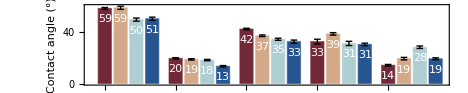

```mathematica
bc = BarChart[data,ChartElementFunction->errorBar["Rectangle"],ChartLabels->{ {"advancing glass", "receding glass", "equilibrium glass", "advancing sup",  "equilibrium sup"}, {20, 25, 30, 35}},ChartStyle->(ColorData["RedBlueTones"][#]&/@Range[0,1,0.33]), BaseStyle->Directive[Black,FontSize->10], Frame->True,FrameStyle->Black, AspectRatio->1/5, ImageSize->72*6.5, FrameLabel->{"", Style["Contact angle (°)", Black]}, LabelingFunction->(Placed[Style[Round[#], White],Top]&)]
```